## Initialization

```mathematica
If[FileExistsQ["~/home-uni/algebra/packages"],BaseDir="~/home-uni",BaseDir="~"];
SetDirectory[BaseDir<>"/papers/sterile-nu/sim"];
$Path=Append[$Path,BaseDir<>"/algebra/packages"];
<<KPTools.m;
```

## Reproduction of the MC simulations from 1609.07803, sec. 4.1 (unfinished)

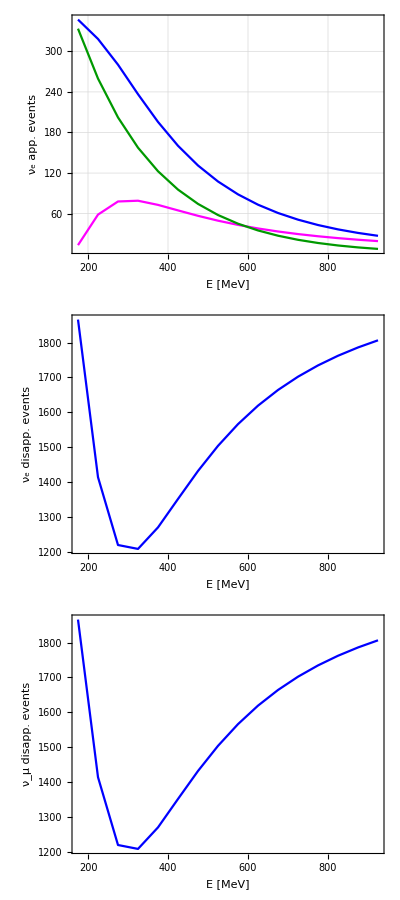

```mathematica
RR=Union[NN,{dmsq->0.75 eV^2,Ue4sq->0.1,Uμ4sq->0.1}];
app=1;
disappE=2;
disappμ=3;

BG[app][E_]:=800 Exp[-E/(200MeV)];
Sig[app][E_,dmsq_,Ue4sq_,Uμ4sq_]:=2000 *4Ue4sq Uμ4sq Sin[(dmsq*500meter)/(4E)]^2;
BG[disappE][E_]:=0;
Sig[disappE][E_,dmsq_,Ue4sq_,Uμ4sq_]:=2000 *(1-4Ue4sq Sin[(dmsq*500meter)/(4E)]^2);
BG[disappμ][E_]:=0;
Sig[disappμ][E_,dmsq_,Ue4sq_,Uμ4sq_]:=2000 *(1-4Uμ4sq Sin[(dmsq*500meter)/(4E)]^2);
BinWidth=50MeV;
BinBoundaries=Range[200MeV,1000MeV,BinWidth];
BinBoundaries=Range[150MeV,950MeV,BinWidth]; 
				(* I think this is what Conrad and Shaevitz actually do,
				   even though it contradicts what they write *)
BinCenters=MapThread[Mean[{#1,#2}]&,{BinBoundaries⟦1;;-2⟧,BinBoundaries⟦2;;-1⟧}];

For[i=1,i≤3,i++,
PlotListBG[i]=Table[{En/MeV,BG[i][En]}//.RR,{En,BinCenters}];
PlotListSig[i]=Table[{En/MeV,Sig[i][En,dmsq,Ue4sq,Uμ4sq]}//.RR,{En,BinCenters}];
PlotListSigBG[i]=Table[{En/MeV,BG[i][En]+Sig[i][En,dmsq,Ue4sq,Uμ4sq]}//.RR,{En,BinCenters}];
];
Grid[{{Show[
ListPlot[PlotListSig[app],Joined->True,PlotStyle->Magenta],
ListPlot[PlotListSigBG[app],Joined->True,PlotStyle->Blue],
ListPlot[PlotListBG[app],Joined->True,PlotStyle->RGBColor[0,.6,0]],
PlotRange->All,AspectRatio->0.3,
FrameLabel->{"E [MeV]","ν_e app. events"},GridLines->Automatic
]},
{Show[
ListPlot[PlotListSigBG[disappE],Joined->True,PlotStyle->Blue],
PlotRange->{0,All},AspectRatio->0.3,
FrameLabel->{"E [MeV]","ν_e disapp. events"}
]},
{Show[
ListPlot[PlotListSigBG[disappμ],Joined->True,PlotStyle->Blue],
PlotRange->{0,All},AspectRatio->0.3,
FrameLabel->{"E [MeV]","ν_μ disapp. events"}
]}
}]
```

```mathematica
(* Pseudo-experiments *)
For[i=1,i≤3,i++,
PseudoData[i]=Transpose[RandomVariate[PoissonDistribution[#],1000]&/@PlotListSigBG[i]⟦All,2⟧];
];
```

dof (app, disapp e, disapp μ) = {15.9928,15.8042,16.2192}

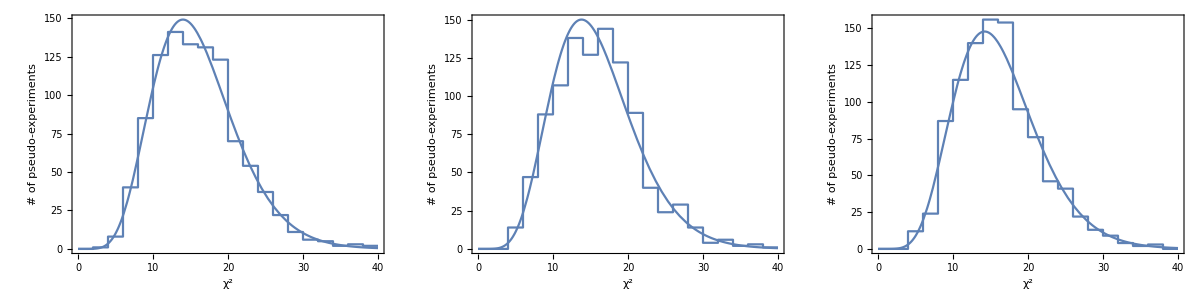

```mathematica
ChiSq[i_][data_,dmsq_,Ue4sq_,Uμ4sq_,ABG_]:=Module[{pred},
pred=(1+ABG)BG[i][#]+Sig[i][#,dmsq,Ue4sq,Uμ4sq]//.NN&/@BinCenters;
Return[Sum[2(pred⟦j⟧-data⟦j⟧+data⟦j⟧Log[data⟦j⟧/pred⟦j⟧])+ABG^2/0.15^2//.NN,{j,1,Length[data]}]]
];
χ2Max=40;
χ2Bins=20;
For[i=1,i≤3,i++,
{ChiSqHisto[i],ChiSqBinned[i]}=KPHistogram[ChiSq[i][#,0.75,0.1,0.1,0]&/@PseudoData[i],0,χ2Max,χ2Bins,ReturnRawData->True];
ChiSqBinned[i]={#⟦1⟧+χ2Max/χ2Bins/2,#⟦2⟧}&/@ChiSqBinned[i]⟦1;;-2⟧;

dofFit[i]=NonlinearModelFit[ChiSqBinned[i],Length[PseudoData[i]]*χ2Max/χ2Bins*
PDF[ChiSquareDistribution[dof]][χ2],{{dof,10}},χ2,
VarianceEstimatorFunction->(1&),Weights->(If[#>0,1/#,0]&/@ChiSqBinned[i]⟦All,2⟧)]["BestFitParameters"];
];
Print["dof (app, disapp e, disapp μ) = ",dof/.{dofFit[app],dofFit[disappE],dofFit[disappμ]}];
Grid[{Table[
Show[Plot[Length[PseudoData[i]]*χ2Max/χ2Bins*PDF[ChiSquareDistribution[dof]][χ2]/.dofFit[i],{χ2,0,χ2Max}],
ChiSqHisto[i],FrameLabel->{"χ^2","# of pseudo-experiments"},ImageSize->300],{i,1,3}]}]
```

```mathematica
For[i=1,i≤5,i++,
ChiSqList[i]=FindMinimum[ChiSq[i][#,dmsq,Ue4sq,Uμ4sq,ABG],
{{ABG,0.1},{dmsq,1},{Ue4sq,0.1},{Uμ4sq,0.1}}]⟦1⟧&/@PseudoData[i];//Quiet
];
disappAll=4;
combined=5;
PG=6;
ChiSqList[disappAll]=MapThread[FindMinimum[ChiSq[disappE][#1,dmsq,Ue4sq,Uμ4sq,ABG]+
ChiSq[disappμ][#2,dmsq,Ue4sq,Uμ4sq,ABG],{{ABG,0.1},{dmsq,1},{Ue4sq,0.1},{Uμ4sq,0.1}}]⟦1⟧&,{PseudoData[disappE],PseudoData[disappμ]}];//Quiet
ChiSqList[combined]=MapThread[FindMinimum[ChiSq[app][#1,dmsq,Ue4sq,Uμ4sq,ABG]+
ChiSq[disappE][#2,dmsq,Ue4sq,Uμ4sq,ABG]+ChiSq[disappμ][#3,dmsq,Ue4sq,Uμ4sq,ABG],
{{ABG,0.1},{dmsq,1},{Ue4sq,0.1},{Uμ4sq,0.1}}]⟦1⟧&,{PseudoData[app],PseudoData[disappE],PseudoData[disappμ]}];//Quiet
ChiSqList[PG]=ChiSqList[combined]-ChiSqList[app]-ChiSqList[disappAll];
```

dof (app, disapp e, disapp μ, disapp all, combined,PG) = {14.0126,13.9638,14.2495,29.1575,45.0456,2.04506}

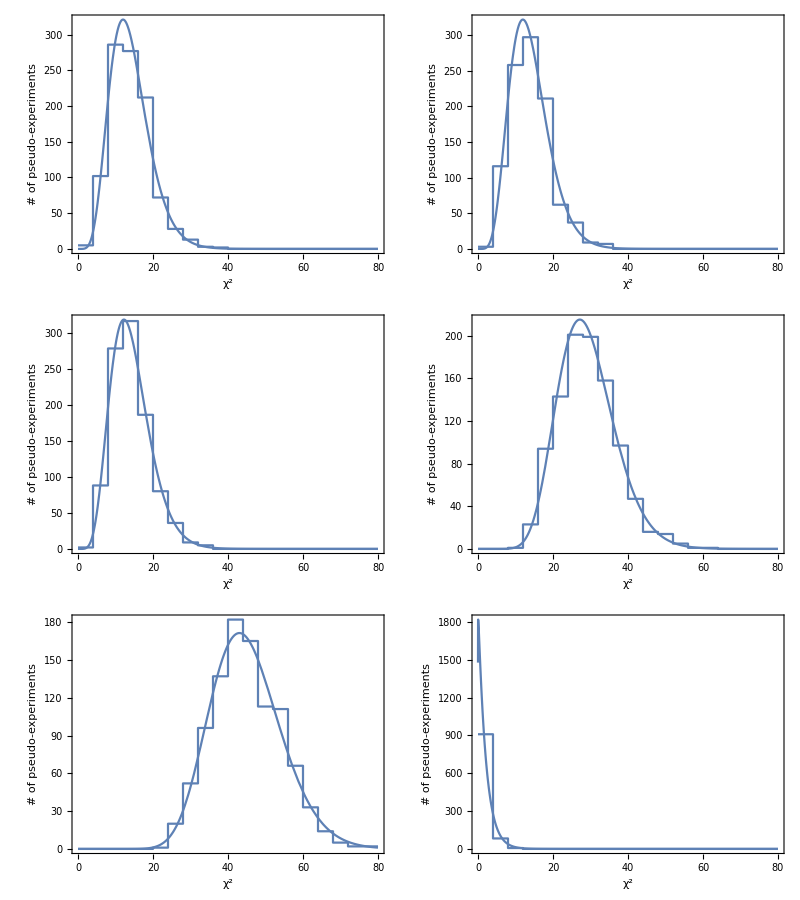

```mathematica
χ2Max=80;
χ2Bins=20;
For[i=1,i≤6,i++,
{ChiSqHisto[i],ChiSqBinned[i]}=KPHistogram[ChiSqList[i],0,χ2Max,χ2Bins,ReturnRawData->True];
ChiSqBinned[i]={#⟦1⟧+χ2Max/χ2Bins/2,#⟦2⟧}&/@ChiSqBinned[i]⟦1;;-2⟧;

dofFit[i]=NonlinearModelFit[ChiSqBinned[i],Length[PseudoData[1]]*χ2Max/χ2Bins*
PDF[ChiSquareDistribution[dof]][χ2],{{dof,If[i<6,30,5]}},χ2,
VarianceEstimatorFunction->(1&),Weights->(If[#>0,1/#,0]&/@ChiSqBinned[i]⟦All,2⟧)]["BestFitParameters"];
];
Print["dof (app, disapp e, disapp μ, disapp all, combined,PG) = ",dof/.{dofFit[app],dofFit[disappE],dofFit[disappμ],dofFit[disappAll],dofFit[combined],dofFit[PG]}];
Grid[Partition[Table[
Show[Plot[Length[PseudoData[1]]*χ2Max/χ2Bins*PDF[ChiSquareDistribution[dof]][χ2]/.dofFit[i],{χ2,0,χ2Max}],
ChiSqHisto[i],FrameLabel->{"χ^2","# of pseudo-experiments"},ImageSize->300],{i,1,6}],UpTo[2]]]
```